```mathematica
xplane = InfinitePlane[{{0,0,0},{0,0,1},{0,1,0}}]
yplane = InfinitePlane[{{0,0,0},{0,0,1},{1,0,0}}]
zplane = InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}]
```

InfinitePlane[{{0,0,0},{0,0,1},{0,1,0}}]

InfinitePlane[{{0,0,0},{0,0,1},{1,0,0}}]

InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}]

```mathematica
FigureXYZslice=SliceVectorPlot3D[{x y-y z-y,x-x y,y z-z},{yplane,xplane,zplane},{y,0,4},{x,0,4},{z,0,4},
VectorScale->{Tiny,Automatic,None},
VectorColorFunction->"DarkRainbow",
Ticks->None,
AxesLabel->
{Style["y",Bold,FontSize->24],Style["x",Bold,FontSize->24],Style["z",Bold,FontSize->24]},
Boxed->False,
PlotTheme->"Monochrome",
PerformanceGoal->"Quality",
ViewPoint->{1.5,1.6,1}]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["XYZ.pdf",FigureXYZslice,"PDF"]
```

C:\Users\Admin\Documents\GitHub\AMATH383Paper

XYZ.pdf

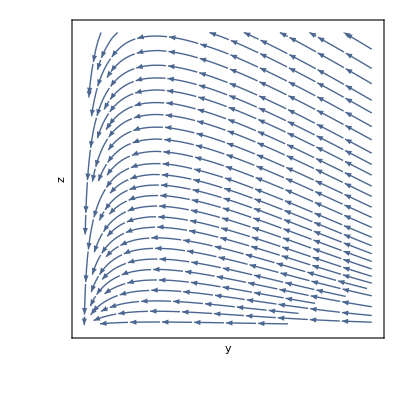

```mathematica
FigureYZplane=StreamPlot[{-y*z-y,y*z-z},{y,0,4},{z,0,4},
FrameLabel->{Style["y",FontSize->24,FontColor->Black],Style["z",FontSize->24,FontColor->Black]},
RotateLabel->False,
PerformanceGoal->"Quality",
FrameTicks->None,
StreamScale->{0.1,.7,None}]
```

```mathematica
Export["YZ.pdf",FigureYZplane,"PDF"]
```

YZ.pdf

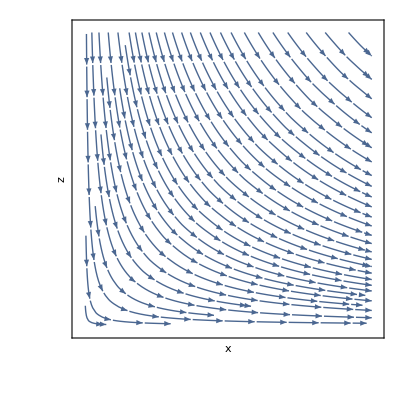

```mathematica
FigureXZplane=StreamPlot[{x,-z},{x,0,4},{z,0,4},
FrameLabel->{Style["x",FontSize->24,FontColor->Black],Style["z",FontSize->24,FontColor->Black]},
RotateLabel->False,
PerformanceGoal->"Quality",
FrameTicks->None,
StreamScale->{0.1,.7,None}]
```

```mathematica
Export["XZ.pdf",FigureXZplane,"PDF"]
```

XZ.pdf

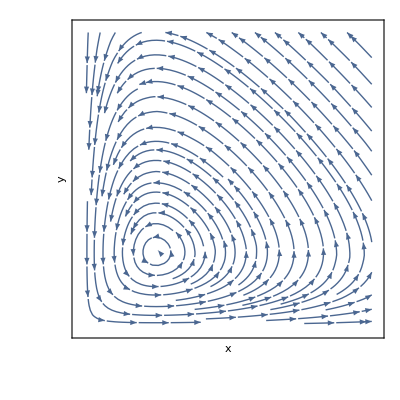

```mathematica
FigureXYplane=StreamPlot[{x-x*y,x*y-y},{x,0,4},{y,0,4},
FrameLabel->{Style["x",FontSize->24,FontColor->Black],Style["y",FontSize->24,FontColor->Black]},
RotateLabel->False,
PerformanceGoal->"Quality",
FrameTicks->None,
StreamScale->{0.1,.7,None}]
```

```mathematica
Export["XY.pdf",FigureXYplane,"PDF"]
```

XY.pdf